H(ⅉω)= 40/((1+(ⅈ ω)/80) (1+(ⅈ ω)/60) (1+(ⅈ ω)/40) (1+(ⅈ ω)/20))

|H(ω)| = (20 Log[40])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/80]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/60]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/40]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/20]])/Log[10]

|ϕ(ω)| = -(180 ArcTan[ω/80])/π-(180 ArcTan[ω/60])/π-(180 ArcTan[ω/40])/π-(180 ArcTan[ω/20])/π

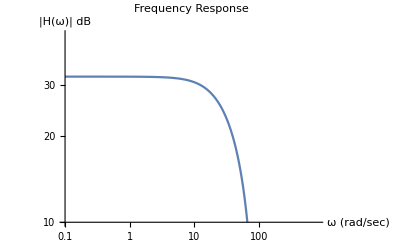

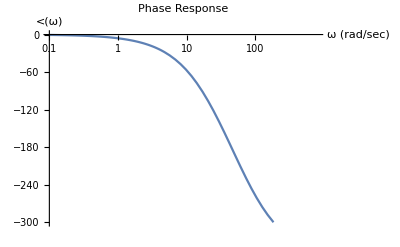

```mathematica
(*Start of Program*)
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];
n = Input["Enter The Number Of Poles"];
listOfPoles =Table[Input["Enter The Value Of A Pole"],n];
listOfTerms=20*Log[10,Abs[(1+(ⅉ ω)/#)&[listOfPoles]]];
listOfPhases=(1/#)&[listOfPoles];
largestPole=Max[listOfPoles];
(*H=Times@@listOfTerms*)
H[ω_]:=K*Times@@(1/(1+(ⅉ*ω)/#))&[listOfPoles](*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
StringForm["H(ⅉω)= ``",H[ω]]
peakMag = FindMaximum[Abs[H[ω]],ω][[1]];
dB[ω_]:=20*Log[10,K]+(Plus@@-listOfTerms)
ϕ[ω_]:=Arg[K]+(Plus@@-(180/π*ArcTan[ω*#]&[listOfPhases]))
StringForm["|H(ω)| = ``", dB[ω]]
StringForm["|ϕ(ω)| = ``", ϕ[ω]]
LogLogPlot[dB[ω],{ω,0.1,10*largestPole},PlotRange->{{0.1,10*largestPole},{10,28*Log[10,K]}},PlotLabel->"Frequency Response", AxesLabel->{"ω (rad/sec)","|H(ω)| dB"}]
LogLinearPlot[ϕ[ω], {ω,0.1,10*largestPole},PlotRange->{{0.1,10*largestPole},{-300,0}},PlotLabel->"Phase Response", AxesLabel->{"ω (rad/sec)","<(ω)"}]
```